Nathan Magari
805505312
natemagari@g.ucla.edu
HW2

{y[t]→H+(g m (m-ⅇ^(-(b t)/m) m-b t))/b^2}

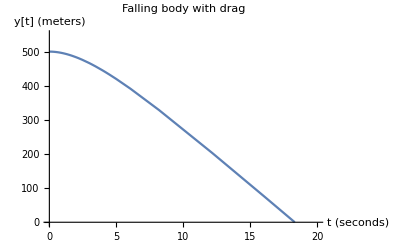

```mathematica
(*PROBLEM I*)
Remove["Global`*"] //Quiet
SetAttributes[{g, b,H,m},Constant];
$Assumptions={Element[{g,b,H,m},Reals] && g > 0 && b > 0 && H > 0 && m>0};
eqnlist = {{y''[t] + (b/m) y'[t] + g == 0},{y[0] == H},{y'[0]==0}};
soln = DSolve[eqnlist,y[t],t][[1]]//FullSimplify
y[t_] = y[t]/.soln;
g := 10
m := 10
b := 3
H := 500
Plot[y[t],{t,0,200}, PlotRange->{{0,20},{0,550}},AxesLabel->{"t (seconds)","y[t] (meters)"},PlotLabel->"Falling body with drag"]
```

```mathematica
(*PROBLEM II*)
Remove["Global`*"]//Quiet
SetAttributes[{δ, L,k,m1,m2},Constant];
diffeq1= {m1 q1''[t] + k q1[t] -k q2[t] == -k L};
diffeq2 = {m2 q2''[t] + k q2[t] -k q1[t] == k L};
init1 = {q1'[0] == 0};
init2 = {q2'[0] == 0};
init3 = {q1[0] == 0};
init4 = {q2[0] == L + δ};
eqnlist = {diffeq1,diffeq2,init1,init2,init3,init4};
funclist = {q1[t],q2[t]};
soln = DSolve[eqnlist,funclist,t][[1]]//FullSimplify
q1[t_] = q1[t]/.soln;
q2[t_] = q2[t]/.soln;
qcm[t_] = (m1 q1[t] + m2 q2[t])/(m1+m2);
L:=5;
m1:=3;
m2:=7;
k:=4; 
δ:=3;
Plot[{q1[t],q2[t],qcm[t]},{t,0,20}, AxesLabel->{"Time","Distance"},PlotLabels ->{"q1[t]","q2[t]","q_cm[t]"},PlotLabel->"Two mass oscillator"]
```

{q1[t]→-(m2 δ (-1+Cosh[(k (m1+m2) t)/(√(-k m1 m2 (m1+m2)))]))/(m1+m2),q2[t]→(L (m1+m2)+m2 δ+m1 δ Cosh[(k (m1+m2) t)/(√(-k m1 m2 (m1+m2)))])/(m1+m2)}

-Graphics-

ⅇ^(-0.0530516 t) (-0.2419 Cos[0.395399 t]+6.10118 Sin[0.395399 t])

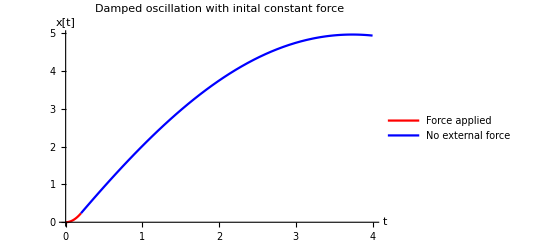

```mathematica
(*PROBLEM III*)
Remove["Global`*"]//Quiet
τ = 1.;
ω = τ/(2*Pi);
β = ω/3.;
a = 12;
f = 0.2;
diffeq1 = {x1''[t] + 2 β x1'[t] + ω^2 x1[t] == a};
init11 = {x1[0] ==0};
init12 = {x1'[0] == 0};
eqnlist1 = {diffeq1,init11,init12};
soln1 = DSolve[eqnlist1,x1[t],t][[1]]//FullSimplify;
x1[t_] = x1[t]/.soln1;
diffeq2 = {x2''[t] + 2 β x2'[t] + ω x2[t] == 0};
init21 = {x2[f τ] ==x1[f τ]};
init22 = {x2'[f τ] ==x1'[f τ]};
eqnlist2 = {diffeq2,init21,init22};
soln2 = DSolve[eqnlist2,x2[t],t][[1]]//FullSimplify;
x2[t_] = x2[t]/.soln2
p1=Plot[x1[t],{t,0,0.2},PlotStyle->Red];
p2=Plot[x2[t],{t,0.2,4},PlotStyle->Blue,PlotLegends -> LineLegend[{Red,Blue},{"Force applied", "No external force"}]];
Show[p1,p2,PlotRange->All,PlotLabel->"Damped oscillation with inital constant force",AxesLabel->{"t","x[t]"}]
```